```mathematica
(*************************************************************************************)
```

This notebook serves as an example of the IMF method in action, a method developed by Craig McRae at the University of Manitoba under the Advisement of Dr. Peter Blunden, to fit generally non-linear models of physical observables, simultaneously to multiple kinds of data with both offset (additive) and scale (multiplicative) uncertainties in a statistically sound way. It is an extension of the NNPDF’s ‘t0’ method.  The thesis explaining the method in great detail may be found at “https://mspace.lib.umanitoba.ca/handle/1993/37116”. 

This example has a particular model in mind, and as such to use it in general one will need to modify the code in order to employ their particular model. The fitting procedure however should work rather generally once the relevant data and model have been set up correctly.

```mathematica
(*************************************************************************************)
```

## Set up and definitions

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Useful if one wishes to present roots of negatives in a specific way*)
sqrtA[x_]:=If[x<0, Return[-Sqrt[-x]], Return[Sqrt[x]]]
sqrt0[x_]:=If[x<0, 0, Return[Sqrt[x]]]

(* Generates Monte Carlo replication of data assuming an underlying Gaussian distribution;
data - data to Monte Carlo replicate;
ddata - uncertainty in data;
nSims - number of replica data sets to produce;
Return - an array of replicated monte-carlo Gaussian replica data*)
Generate[data_,ddata_, nSims_]:=Module[{replica,Data=data,DData=ddata, Nsims=nSims, Ndat=Length[data],j},
For[j=1;replica={},j≤ Ndat, j++, AppendTo[replica, RandomVariate[NormalDistribution[Data[[j]],DData[[j]]],Nsims]]];
Return[Transpose[replica],Module]
]

(*Same as above except the underlying guassian distibuition the replicas come from stops at 0. Really no difference for all the data we have*)
GenerateCorrectly[data_,ddata_, nSims_]:=Module[{Data=data,DData=ddata, Nsims=nSims, Ndat=Length[data], j, replica},
For[j=1;replica={},j≤ Ndat, j++, AppendTo[replica, RandomVariate[TruncatedDistribution[{0,∞},NormalDistribution[Data[[j]],DData[[j]]]],Nsims]]
];
Return[Transpose[replica],Module]
]

(*Sometimes useful, wraps each entry of ana array into its own sub array*)
Vectorize[x_]:= Return[Table[{x[[i]]},{i,1,Length[x]}]];
```

```mathematica
(*MateX preamble*)
<<MaTeX`
```

```mathematica
texStyle={FontFamily->"Times",FontSize->22};
(* I used txfonts (Times) to match fonts, but if you want standard LaTeX font drop Preamble. *)
SetOptions[MaTeX,FontSize->22,Magnification->1,Preamble->{"\\usepackage{txfonts}"}];
```

```mathematica
(*Using the same seed ensures stochastic results are exactly reproducible (such as MC replications)*)
SeedRandom[2];
```

## Data and Physics

In general this section will require modification depending on the particular physics involved. Independent variables, uncertainties etc.
It is designed to read in N experiments of the same kind of data, and make sets of non-rectangular arrays which have two indices: Theta[[1,2]] for example would the relevant angle for the first experiment’s second data point, etc. It anticipates data in standard CSV format (excel columns with headers). 
Unless stated otherwise, all data, variables etc should have this same shape once all data has been read in. The setup from here on assumes the error is point to point except for normalization error, so code for handling an additive covariance matrix would need to be put in if needed (but should be largely compatible, set dFitData to the root of the covariance matrix’s diagonal, and then everything is the same except the need to modify the building of the total IMF chi-square which currently assumes a diagonal additive covariance matrix).

```mathematica
(*Read in data*)
Corr=1;(*Turns TPE corrections on(1) and off(0)*)
SetDirectory[NotebookDirectory[]];
FitData={}; (* Data to be fit *)
dFitData={}; (*additive uncertainty in fit data *)
QQ={}; (* Q^2 of particlar data *)
eps = {}; (* ϵ of particlar data *)
Enorm={}; (* Normalization uncertainty, SHOULD BE A SINGLE 1xN ARRAY*)
Esyst={}; (* systematic uncertainty *)
Estat={}; (* statistical uncertainty *)
E1={}; (* Incoming beam energy *)
Theta={}; (* scattering angle in lab frame *)
Sigma={}; (* differential cross section *)
dSigma={}; (* uncertainty of diff cross section *)
ThetaR={}; (* scattering angle in radians *)
delAll={}; (* Corrective exponent *)
CrossNum=9; (* Number of cross section data sets used here *)
For[i=1,i≤ CrossNum,i++,dataLoad=Import["../Data/GMp/CSDataPGB_CM"<>ToString[i]<>".csv"];
curr=Transpose[Drop[dataLoad,1]];
AppendTo[Sigma,Vectorize[curr[[8]]]];
AppendTo[dSigma,Vectorize[curr[[9]]]];
AppendTo[QQ,Vectorize[curr[[2]]]];
AppendTo[eps,Vectorize[curr[[3]]]];
AppendTo[E1,Vectorize[curr[[4]]]];
AppendTo[Theta,Vectorize[curr[[5]]]];
AppendTo[Enorm,curr[[12,1]]]; (**)
AppendTo[delAll,Vectorize[curr[[19]]]]
]
ThetaR=Theta*π/180;
sin2t2=Sin[ThetaR/2]^2;
```

```mathematica
(*Constants*)
M=0.938272046; (*Proton mass GeV*)
Alfa=1/137.035999074; (*Fine structure constant*)
mu=2.792847356; (*Magnetic moment in nuclear megnetons*)
mu2=mu^2;
hc2=389379.338; (* conversion from nb to GeV^(-2) *)

(*Other useful kinematic variables*)
Tau =QQ/4/M^2; (*Vector of Tau values*)
gd = 1/(1+Q2/0.71)^2; (*function of Q2*)
GD = 1/(1+QQ/0.71)^2; (*Vector of specific GD values at given QQ values*)
E3=E1-QQ/2/M; (*Outgoing electron energy*)
eeps=((1-sin2t2)*M*(M+2*E1*sin2t2))/(M^2+M*(2*E1+M)*sin2t2+2*E1*(E1+M)*sin2t2^2); (*epsilon, aleady loaded in as 'eps', can check they match for a sanity check*)
Mott=Alfa^2 (1-sin2t2)/(2*E1*sin2t2)^2*E3/E1; (*Mott cross section*)
FitData=eps(1+Tau)*(Sigma*Exp[-delAll*Corr]/(hc2*Mott)); (*reduced cross section, TPE-corrected if corr=1*)
dFitData=eps(1+Tau)*(dSigma*Exp[-delAll*Corr]/(hc2*Mott)); (*reduced cross section error*)
```

## Replica Data

Now that we know our data, we are ready to build the scaffolding for the Monte-Carlo replicas. These will actually be built during the main IMF loop.
‘Replica’ will be an array of replica data 
‘Norms’ will be an array of normalization factors, depending on normalization uncertainty
‘Sims’ is how many simulated data sets to construct at every iteration of the IMF. This has a significant impact on run time, but should be at least 50 for good statistics

```mathematica
(*Make vector for Replica data and guassian norms*)
Replica =Table[{},{i, Length[FitData]}];
Norms=Table[{},{i, Length[FitData]}];
(*Number of replicas to make ('simulations')*)
Sims=100;
```

```mathematica
(*Store chi-square's to check if 10 iterations is enough for the chi-squares to be essentially the same*)
(*This is a rather good proxy for input and output models of the observable being equal, but one should always check*)
chis={};
```

## Building a Model

This section is all you baby:
 ‘params’ need to be a flat list of variables, like {a1, a2,...,b1,...,bn} which your model depends on (NOT the independent variables, like angle or energy). 
 ‘nparams’ is just the number of params.
‘Model’ needs to be an array of the exact same shape and dimensions as your FitData. I.e. ‘Model’  is your model evaluated at the physics for each data point 
(each entry of ‘Model’ should only depend on the free parameters).

```mathematica
(*Gramolin Model at relevant data points*)
GE2 = GD^2*(1-a[1]*Tau-a[2]*Tau^2-a[3]*Tau^3); 
GM2 =GD^2*(1-b[1]*Tau-b[2]*Tau^2-b[3]*Tau^3);
```

```mathematica
(*Model of the observable in FitData, GM normalized to 1 so dont forget the mu2*)
(*Model = Table[{},{i,CrossNum}] ;*)
Model = (eps*GE2+Tau*(mu2)*GM2);
(*
If you plan to simultaneously fit data which is modelled differently;
you can do so by modifying the model in those spots, below is if we were including polarization ratio data*)
(*Model[[CrossNum+1;;]] = (mu2)GE2[[CrossNum+1;;]]/GM2[[CrossNum+1;;]]);*)
(* This Makes sure the model being fit to the data is the cross section for LT data but R for PT data *)
```

```mathematica
(*parameter list*)
params = {Table[a[i],{i,3}],Table[b[i],{i,3}]}//Flatten;
nparams = Length[params];
```

## The main IMF Loop

Below is the main work of the notebook, and assuming everything has been set up correctly (FitData, dFitData, and Model are all the same dimensions), the only thing left is to make a ‘guess’ for the parameters, implemented as a replacement rule. In the example a dipole is reasonable. If you find poor convergence of your fits, especially for non-linear models, try varying the initial guess, or increasing the count of the loop.

```mathematica
guess={a[1]->0,a[2]->0,a[3]->0,b[1]->0,b[2]->0,b[3]->0}; (*Set initial guess to dipole*)
```

```mathematica
(*
This is the main loop of the IMF method;
It loops a specified number of times fitting model to data, and feeding the previous average parameter in as the next guess;
The fitted models along the way are stored in "outIMF.m"
*)
For[count=1; guesses = {}, count≤ 10,count++,
(*
This for loop builds the Inverse of the IMF-Method Covariance matrix;
This is required to build the general chi-square*)
For[i=1;InvCov=Table[0,{m,CrossNum}],i≤ CrossNum,i++,
InvCov[[i]]=Inverse[DiagonalMatrix[(Transpose[dFitData[[i]]][[1]])^2]+Table[((((Transpose[Model[[i]]][[1]])[[j]])*((Transpose[Model[[i]]][[1]])[[k]]))/.guess)*Enorm[[i]]^2,{j,1,Length[dFitData[[i]]]},{k,1,Length[dFitData[[i]]]}]];
];

(*Loop for building replica data arrays*)
For[i=1, i≤Length[FitData],i++, Replica[[i]] = GenerateCorrectly[Transpose[FitData[[i]]][[1]],Transpose[dFitData[[i]]][[1]], Sims]];
(*Loop for building normally distributed normalization prefactors*)
For[i=1, i≤ CrossNum,i++, Norms[[i]] = RandomVariate[NormalDistribution[1,Enorm[[i]]],Sims]];
(*
Assuming your polarization ratio data comes after your cross section data;
This code just builds prefactors that are all 1 on that data, so the code may run uniformly on all data;
only needed if fitting data which has no scale uncertainty*)
(*For[i=CrossNum+1, i≤ Length[FitData],i++, Norms[[i]] = ((RandomVariate[NormalDistribution[1,1],Sims])*0+1)];*)

(*An array storing the analytic expression for chi-square of each replica*)
chi=Table[0,{m,Sims}];
(*Loop over each replica data set*)
For[rep=1,rep≤Sims,rep++,
(*Build the IMF chi-square for data with normalization uncertainty*)
For[i=1,i≤ CrossNum,i++,chi[[rep]]+=(Transpose[(Vectorize[Norms[[i,rep]]*Replica[[i,rep]]]-Model[[i]])].InvCov[[i]].((Norms[[i,rep]]*Replica[[i,rep]]-Model[[i]])))[[1,1]]
];
(*Build the usual chi-square for data without norm uncertainty*)
(*This part will simply be skipped if there is no PT data*)
For[i=CrossNum+1,i≤ Length[FitData],i++,
For[j=1,j≤ Length[FitData[[i]]],j++,
chi[[rep]]+=Total[ (Replica[[i,rep,j]]-Model[[i,j,1]])^2/(dFitData[[i,j,1]])^2]
];
];
];

(*Now we have every replica's chi-square, time to minimize them*)
(*"SetSharedVariable" and "ParallelDo" are for parallelizing this process*)
(*Sometimes the overhead of setting up paralellization is slower than if you just did things normally, do what works*)
SetSharedVariable[guesses];
guesses={};
(*Loop for minimizing replica χ2, and collecting best fit parameters into the list "guesses"*)
ParallelDo[
AppendTo[guesses, ( NMinimize[chi[[k]],params][[2]])[[Range[nparams],2]]]
,{k,Sims}];

(*This Constructs a replacement rule from the mean of replica minima*)
(*This rule is the next guess we'll use in the next iteration*)
guess=Transpose[{params,Mean[guesses]}];
For[n = 1,n≤nparams,n++, guess[[n,0]]=Rule];

(*What is the chi-square of this new mean of replica parameters?*)
For[i=1;χ=0,i≤ CrossNum,i++,χ+=(Transpose[FitData[[i]]-Model[[i]]/.guess].InvCov[[i]].((FitData[[i]]-Model[[i]]/.guess)))[[1,1]]
];

(*Report chi-square, Current best guess/fit params, and Covariance matrix of that fit in "outIMF.m"*)
AppendTo[chis,χ];
ModelErr=Covariance[guesses];
Save["outIMF.m",{chis,guess,ModelErr}]
(*Finished IMF Loop*)]
```

```mathematica
(*
If everything in outIMF.m looks good, i.e. chi-squares are constant, model staying aporoximately the same;
We can move on to analyze the fit! ;
'guess' should contain the replacement rule for the models best fit parameters
*)
```

## Constructing Models with Error

Data has error, so our fits to that data ought to reflect that. The whole point of the project is that we are able to reliably characterize the error of a non-linear model fit to data with additive and multiplicative uncertainty. The convenience of using a Monte-Carlo method to fit, is that the distribution of parameters on the MC data give us directly a distribution whose covariance can be readily found (in the last section stored as ‘ModelErr’). This combined with a hard days honest error propagation (necessarily based upon and modified due to the structure of your model), allow us to find the correct error bands on the underlying functions of our model.

```mathematica
(*Following section builds the functions, and the 1σ error bands of functions*)
(*'vectors' for GE and GM wrt the covariance matrix for the parameters*)
(*The parameters serve as the basis, coefficients as vector components, the covariance matrix is essentially an inner product*)
(*f_i here specifically are those coefficients on the parameters, substituded in later*)
VecE={{f1},{f2},{f3},{0},{0},{0}};
VecM={{0},{0},{0},{f4},{f5},{f6}};
(*Build ge2 and gm2 modulo gd^2*)
CentralE =(1-(Transpose[VecE].params)[[1]]);
CentralM =(1-(Transpose[VecM].params)[[1]]);
```

```mathematica
ge2 = FullSimplify[((CentralE/.guess)/.{f1-> (Q2/4/M^2), f2-> (Q2/4/M^2)^2, f3-> (Q2/4/M^2)^3})]//Chop;(*Corefficients are just powers of τ*)
gm2 = FullSimplify[((CentralM/.guess)/.{f4-> (Q2/4/M^2), f5-> (Q2/4/M^2)^2, f6-> (Q2/4/M^2)^3})]//Chop;
```

```mathematica
(*Takes into account the fully correlated sum of the three parameters uncertainties for a[i], or b[i]. The index [[1,1]] is only there because the covariance inner product gives a 1x1 matrix*)
SqErrE2= FullSimplify[(((Transpose[VecE].ModelErr.VecE)[[1,1]]//FullSimplify//Expand//Chop)/.{f1-> Q2/4/M^2, f2-> (Q2/4/M^2)^2, f3-> (Q2/4/M^2)^3})]//Chop; 
SqErrM2= FullSimplify[(((Transpose[VecM].ModelErr.VecM)[[1,1]]//FullSimplify//Expand//Chop)/.{f4-> Q2/4/M^2, f5-> (Q2/4/M^2)^2, f6-> (Q2/4/M^2)^3})]//Chop;
SqErrEM2=1/(gm2)^2(SqErrE2+(ge2/gm2)^2*SqErrM2)/.guess;(*Usual uncertainty propogation of the quotient Ge2/Gm2*)
```

```mathematica
(*Cross section built from the fits divided by τ, implicitly divided by gd^2 since both ge2 and gm2 are*)
(*σ = (ϵ ge2+mu2*gm2 (Q2/4/M^2) )/(Q2/4/M^2);*)
(*Because σ is linear in the paramerers, its uncertainty is just the correlated sum, properly accounting for the coefficients*)
(*σerr =FullSimplify[Sqrt[(((Transpose[VecE+VecM].ModelErr.(VecE+VecM))[[1,1]]//FullSimplify//Expand//Chop)/.{f1-> ϵ, f2->ϵ(Q2/4/M^2), f3->ϵ(Q2/4/M^2)^2,f4->mu2(Q2/4/M^2), f5-> mu2(Q2/4/M^2)^2, f6-> mu2(Q2/4/M^2)^3})]//Chop];*)
```

```mathematica
(*DONE BUILDING IMF FITS!!!!!!*)
```

```mathematica
(*************************************************************************************)
```

## The Penalty Trick

For completeness, the following section has the traditional ‘Penalty trick’ method of fitting the data.

```mathematica
(*Build penalty chi-square and minimize all parameters*)
n=.; (*Reset n*)
params={a[1],a[2],a[3],b[1],b[2],b[3],n[1],n[2],n[3],n[4],n[5],n[6],n[7],n[8],n[9]};
(*build penalty trick chi-sqaure*)
For[i=1; χ=0,i≤ CrossNum,i++,
For[j=1,j ≤ Length[FitData[[i]]],j++,
χ+=(n[i]*FitData[[i,j,1]]-Model[[i,j,1]])^2/(dFitData[[i,j,1]])^2; 
];
χ+= (n[i]-1)^2/(Enorm[[i]])^2
];
χ;
```

```mathematica
(*Often when n is larger or the function is non-linear in the params, different numerical methods find different minima*)
(*So we try all methods, and pick the smallest*)
penaltyBestFit=(NMinimize[χ,params,Method->#]&/@{"NelderMead","DifferentialEvolution","SimulatedAnnealing","RandomSearch"})
```

{{60.09,{a[1]→0.371544,a[2]→-0.0184491,a[3]→0.19057,b[1]→-0.424971,b[2]→0.385949,b[3]→-0.099179,n[1]→1.00548,n[2]→1.00272,n[3]→0.958553,n[4]→0.978082,n[5]→0.998682,n[6]→1.01685,n[7]→1.06522,n[8]→1.00459,n[9]→0.994538}},{60.09,{a[1]→0.371544,a[2]→-0.0184491,a[3]→0.19057,b[1]→-0.424971,b[2]→0.385949,b[3]→-0.099179,n[1]→1.00548,n[2]→1.00272,n[3]→0.958553,n[4]→0.978082,n[5]→0.998682,n[6]→1.01685,n[7]→1.06522,n[8]→1.00459,n[9]→0.994538}},{60.09,{a[1]→0.371544,a[2]→-0.0184491,a[3]→0.19057,b[1]→-0.424971,b[2]→0.385949,b[3]→-0.099179,n[1]→1.00548,n[2]→1.00272,n[3]→0.958553,n[4]→0.978082,n[5]→0.998682,n[6]→1.01685,n[7]→1.06522,n[8]→1.00459,n[9]→0.994538}},{60.09,{a[1]→0.371544,a[2]→-0.0184491,a[3]→0.19057,b[1]→-0.424971,b[2]→0.385949,b[3]→-0.099179,n[1]→1.00548,n[2]→1.00272,n[3]→0.958553,n[4]→0.978082,n[5]→0.998682,n[6]→1.01685,n[7]→1.06522,n[8]→1.00459,n[9]→0.994538}}}

```mathematica
choice=2; (*Which of the above 4 is smallest?*)
penaltyGuess=penaltyBestFit[[choice]][[2]](*best fit parameters*)
penaltychi=penaltyBestFit[[choice]][[1]];(*penalty chi-sqaure value for those parmeters*)
(*'ModelErr' equivalent for penalty fit. Inverse of the Hessian matrix of the chi-sqaure (chi square has a 1/2 in the definition, we just ignore it when minimizing)*)

(*The covariance matrix matrix of parameters when the model is lienar, is exactly the inverse Hessian of the 
gaussian exponent, which is half the chi-square. When the model is non-linear, we may approximate the covariance matrix
as the inverse Hessian at our best fit parameters (only linear models will in general have a constant Hessian). 
*)
PenaltyErr=Inverse[1/2 D[χ,{params},{params}]]
```

{a[1]→0.371544,a[2]→-0.0184491,a[3]→0.19057,b[1]→-0.424971,b[2]→0.385949,b[3]→-0.099179,n[1]→1.00548,n[2]→1.00272,n[3]→0.958553,n[4]→0.978082,n[5]→0.998682,n[6]→1.01685,n[7]→1.06522,n[8]→1.00459,n[9]→0.994538}

{{0.0401706,-0.0809882,0.0372084,-0.00228463,0.00673566,-0.00327521,-0.000779718,-0.000680781,-0.000542445,-0.000598056,-0.000337755,-0.000911059,-0.000674453,-0.000644367,-0.000767432},{-0.0809882,0.213657,-0.109328,0.000887974,-0.0114002,0.00690449,0.00128999,0.00124288,0.00147085,0.00104259,0.000667102,0.0013577,0.000811364,0.00105332,0.00142142},{0.0372084,-0.109328,0.0615174,0.000236454,0.00473352,-0.00336756,-0.000524247,-0.000538794,-0.000534655,-0.000443683,-0.000287163,-0.000571431,-0.000357723,-0.000483613,-0.000592001},{-0.00228463,0.000887974,0.000236454,0.00160098,-0.00207232,0.000713128,-0.00013499,-0.000140212,-0.000194232,-0.000120723,-0.0000985228,-0.0000938132,-0.000124171,-0.0000723008,-0.000129768},{0.00673566,-0.0114002,0.00473352,-0.00207232,0.00336507,-0.00133674,0.0000826193,0.0000799,0.000126945,0.0000889006,0.0000807383,0.0000333779,0.0000915051,7.69873×10^-6,0.0000576771},{-0.00327521,0.00690449,-0.00336756,0.000713128,-0.00133674,0.000584383,-0.0000112161,-7.72659×10^-6,-0.0000267155,-0.0000199548,-0.000018918,5.71518×10^-6,-0.0000181185,0.0000149757,9.47803×10^-7},{-0.000779718,0.00128999,-0.000524247,-0.00013499,0.0000826193,-0.0000112161,0.00006286,0.0000539195,0.000047441,0.0000445915,0.000029082,0.0000570034,0.0000590103,0.0000438743,0.0000540405},{-0.000680781,0.00124288,-0.000538794,-0.000140212,0.0000799,-7.72659×10^-6,0.0000539195,0.0000615616,0.000049109,0.0000438603,0.000028021,0.0000544116,0.0000578963,0.0000449397,0.0000535799},{-0.000542445,0.00147085,-0.000534655,-0.000194232,0.000126945,-0.0000267155,0.000047441,0.000049109,0.000090836,0.0000398147,0.0000270529,0.0000422376,0.000042516,0.0000361276,0.0000503103},{-0.000598056,0.00104259,-0.000443683,-0.000120723,0.0000889006,-0.0000199548,0.0000445915,0.0000438603,0.0000398147,0.0000785908,0.0000232843,0.0000459801,0.0000485395,0.0000369871,0.0000435682},{-0.000337755,0.000667102,-0.000287163,-0.0000985228,0.0000807383,-0.000018918,0.000029082,0.000028021,0.0000270529,0.0000232843,0.000205421,0.0000282737,0.0000294167,0.0000216085,0.0000280102},{-0.000911059,0.0013577,-0.000571431,-0.0000938132,0.0000333779,5.71518×10^-6,0.0000570034,0.0000544116,0.0000422376,0.0000459801,0.0000282737,0.000115555,0.0000629912,0.0000471117,0.0000542955},{-0.000674453,0.000811364,-0.000357723,-0.000124171,0.0000915051,-0.0000181185,0.0000590103,0.0000578963,0.000042516,0.0000485395,0.0000294167,0.0000629912,0.0000938125,0.0000511207,0.0000564498},{-0.000644367,0.00105332,-0.000483613,-0.0000723008,7.69873×10^-6,0.0000149757,0.0000438743,0.0000449397,0.0000361276,0.0000369871,0.0000216085,0.0000471117,0.0000511207,0.000281295,0.0000442525},{-0.000767432,0.00142142,-0.000592001,-0.000129768,0.0000576771,9.47803×10^-7,0.0000540405,0.0000535799,0.0000503103,0.0000435682,0.0000280102,0.0000542955,0.0000564498,0.0000442525,0.0000609211}}

```mathematica
(*Same deal as above, but more parameters since more normalizations*)
VecE={{f1},{f2},{f3},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}};
VecM={{0},{0},{0},{f4},{f5},{f6},{0},{0},{0},{0},{0},{0},{0},{0},{0}};
CentralE =(1-(Transpose[VecE].params)[[1]]);
CentralM =(1-(Transpose[VecM].params)[[1]]);
```

```mathematica
(*suffix 'pen' applied to all penalty trick versions of the models and errors. Pretty much identical to above but with penalty fit*)
ge2pen = FullSimplify[((CentralE/.penaltyGuess)/.{f1-> (Q2/4/M^2), f2-> (Q2/4/M^2)^2, f3-> (Q2/4/M^2)^3})]//Chop;
gm2pen = FullSimplify[((CentralM/.penaltyGuess)/.{f4-> (Q2/4/M^2), f5-> (Q2/4/M^2)^2, f6-> (Q2/4/M^2)^3})]//Chop;
```

```mathematica
SqErrE2pen= FullSimplify[(((Transpose[VecE].PenaltyErr.VecE)[[1,1]]//FullSimplify//Expand//Chop)/.{f1-> Q2/4/M^2, f2-> (Q2/4/M^2)^2, f3-> (Q2/4/M^2)^3})]//Chop;
SqErrM2pen= FullSimplify[(((Transpose[VecM].PenaltyErr.VecM)[[1,1]]//FullSimplify//Expand//Chop)/.{f4-> Q2/4/M^2, f5-> (Q2/4/M^2)^2, f6-> (Q2/4/M^2)^3})]//Chop;
SqErrEM2pen=1/(gm2pen)^2(SqErrE2pen+(ge2pen/gm2pen)^2*SqErrM2pen)/.penaltyGuess;
```

```mathematica
(*σpen= (ϵ ge2pen+mu2*gm2pen (Q2/4/M^2) )/(Q2/4/M^2);
σerrpen =FullSimplify[Sqrt[(((Transpose[VecE+VecM].PenaltyErr.(VecE+VecM))[[1,1]]//FullSimplify//Expand//Chop)/.{f1-> ϵ, f2->ϵ(Q2/4/M^2), f3->ϵ(Q2/4/M^2)^2,f4->mu2(Q2/4/M^2), f5-> mu2(Q2/4/M^2)^2, f6-> mu2(Q2/4/M^2)^3})]//Chop];*)
```

## Plotting the Fits

```mathematica
(*loaded to plot with Ge/Gm stuff, 28 data points for pol with Q^2 > 1*)
For[i=1,i≤ 9,i++,dataLoad=Import["../Data/GMp/PolDat"<>ToString[i]<>".csv"];
curr=Transpose[Drop[dataLoad,1]];
AppendTo[FitData,curr[[2]]];
AppendTo[dFitData,curr[[3]]];
AppendTo[QQ,curr[[1]]];
AppendTo[eps,0*curr[[1]]];
AppendTo[Enorm,0];
](*For i*)
Pol = Table[Around[(FitData[[CrossNum+1;;]]//Flatten)[[j]],(dFitData[[CrossNum+1;;]]//Flatten)[[j]]],{j,Length[FitData[[CrossNum+1;;]]//Flatten]}];
(*Sqaured pol ratio data, dont forget to propogate uncertainty!*)
Pol2 = Table[Around[((FitData[[CrossNum+1;;]]//Flatten)[[j]])^2,(((2*dFitData[[CrossNum+1;;]])//Flatten)*(FitData[[CrossNum+1;;]]//Flatten))[[j]]],{j,Length[FitData[[CrossNum+1;;]]//Flatten]}];
```

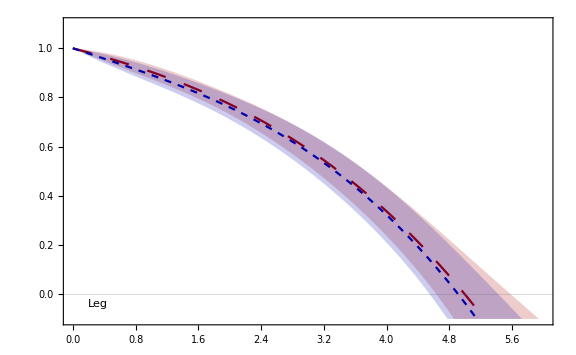

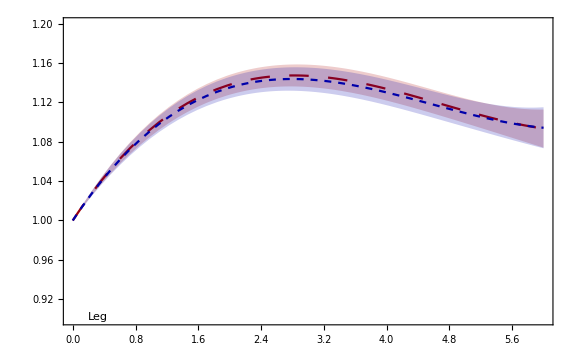

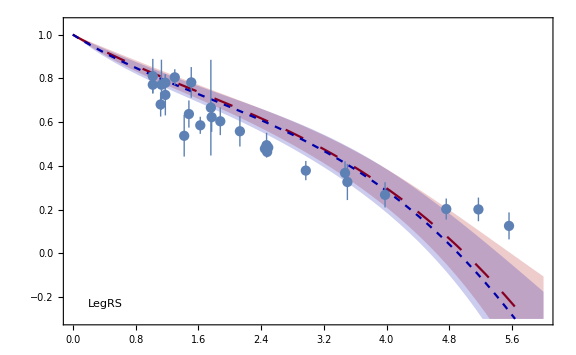

```mathematica
(*Plot Ranges*)
Q2max=6;
Q2min=0;
Erange = {-0.1,1.1};
Mrange = {0.9,1.2};
EMrange = {-0.3,1.05};
(*BUild IMF Method fits in Red*)
(*Usually I keep all my graphics and Legends in another notebook, so they're all in one place*)
Color=Red;
Dash=Large;
plotE2=Plot[{(ge2+Sqrt[SqErrE2]),(ge2-Sqrt[SqErrE2]),ge2},{Q2,Q2min,Q2max}, PlotRange->Erange,Filling->{1-> {2}},FillingStyle->Directive[Darker[Color],Opacity[0.2]], PlotStyle->{None,None,Directive[Darker[Color],Dashing[Dash]]},ImageSize->Large, Frame-> True, FrameStyle->BlackFrame,FrameLabel->Flatten[{MaTeX[{"Q^2~(\\text{GeV}^2)","G_E^2(Q^2)/G_D^2(Q^2)"},Magnification->1.3],None}],BaseStyle->texStyle,Epilog->Text[MaTeX["\\text{}",Magnification->1],{7,.2}], GridLines->{{},{0}}];
plotM2=Plot[{(gm2+Sqrt[SqErrM2]),(gm2-Sqrt[SqErrM2]),gm2},{Q2,Q2min,Q2max}, PlotRange->Mrange,Filling->{1-> {2}},FillingStyle->Directive[Darker[Color],Opacity[0.2]], PlotStyle->{None,None,Directive[Darker[Color],Dashing[Dash]]},ImageSize->Large, Frame-> True, FrameStyle->BlackFrame,FrameLabel->Flatten[{MaTeX[{"Q^2~(\\text{GeV}^2)","G_M^2(Q^2)/\mu^2_p G_D^2(Q^2)"},Magnification->1.3],None}],BaseStyle->texStyle,Epilog->Text[MaTeX["\\text{Z expansion}",Magnification->1],{7,.2}]];
plotEM2=Plot[{ge2/gm2+Sqrt[SqErrEM2],(ge2/gm2-Sqrt[SqErrEM2]),ge2/gm2},{Q2,Q2min,Q2max}, PlotRange->EMrange,Filling->{1-> {2}},FillingStyle->Directive[Darker[Color],Opacity[0.2]], PlotStyle->{None,None,Directive[Darker[Color],Dashing[Dash]]},ImageSize->Large, Frame-> True, FrameStyle->BlackFrame,FrameLabel->Flatten[{MaTeX[{"Q^2~(\\text{GeV}^2)","\mu^2_p G_E^2(Q^2)/G_M^2(Q^2)"},Magnification->1.3],None}],BaseStyle->texStyle,Epilog->Text[MaTeX["\\text{}",Magnification->1],{6.5,1}]];

(*Build Penalty Trick fits in Blue*)
Color = Blue;
Dash = Small;
plotE2pen=Plot[{(ge2pen+Sqrt[SqErrE2pen]),(ge2pen-Sqrt[SqErrE2pen]),ge2pen},{Q2,Q2min,Q2max}, PlotRange->Erange,Filling->{1-> {2}},FillingStyle->Directive[Darker[Color],Opacity[0.2]], PlotStyle->{None,None,Directive[Darker[Color],Dashing[Dash]]},ImageSize->Large, Frame-> True, FrameStyle->BlackFrame,FrameLabel->Flatten[{MaTeX[{"Q^2~(\\text{GeV}^2)","G_E^2(Q^2)/G_D^2(Q^2)"},Magnification->1.3],None}],BaseStyle->texStyle,Epilog->Text[MaTeX["\\text{}",Magnification->1],{7,.2}], PlotLegends->Placed[Leg,{{0.05,0.05},{0.05,0.1}}]];
plotM2pen=Plot[{(gm2pen+Sqrt[SqErrM2pen]),(gm2pen-Sqrt[SqErrM2pen]),gm2pen},{Q2,Q2min,Q2max}, PlotRange->Mrange,Filling->{1-> {2}},FillingStyle->Directive[Darker[Color],Opacity[0.2]], PlotStyle->{None,None,Directive[Darker[Color],Dashing[Dash]]},ImageSize->Large, Frame-> True, FrameStyle->BlackFrame,FrameLabel->Flatten[{MaTeX[{"Q^2~(\\text{GeV}^2)","G_M^2(Q^2)/\mu^2_p G_D^2(Q^2)"},Magnification->1.3],None}],BaseStyle->texStyle,Epilog->Text[MaTeX["\\text{Z expansion}",Magnification->1],{7,.2}], PlotLegends->Placed[Leg,{{0.05,0.01},{0.05,0.1}}]];
plotEM2pen=Plot[{ge2pen/gm2pen+Sqrt[SqErrEM2pen],(ge2pen/gm2pen-Sqrt[SqErrEM2pen]),ge2pen/gm2pen},{Q2,Q2min,Q2max}, PlotRange->EMrange,Filling->{1-> {2}},FillingStyle->Directive[Darker[Color],Opacity[0.2]], PlotStyle->{None,None,Directive[Darker[Color],Dashing[Dash]]},ImageSize->Large, Frame-> True, FrameStyle->BlackFrame,FrameLabel->Flatten[{MaTeX[{"Q^2~(\\text{GeV}^2)","\mu^2_p G_E^2(Q^2)/G_M^2(Q^2)"},Magnification->1.3],None}],BaseStyle->texStyle,Epilog->Text[MaTeX["\\text{}",Magnification->1],{6.5,1}], PlotLegends->Placed[LegRS,{{0.05,0.05},{0.1,0.1}}]];

(*Plot Ge2, Gm2, and  Ge2/Gm2 with pol data*)
Show[plotE2,plotE2pen]
Show[plotM2,plotM2pen]
Show[plotEM2,plotEM2pen,ListPlot[Transpose[{QQ[[CrossNum+1;;]]//Flatten,Pol2}]]]
```